```mathematica
data=Import["/Users/ivandybko/Projects/Numerical_methods/Lab3/src/data/x^2/x^2_64_spline_uniform_grid.txt","Table"];

f[x_]:=10000000000x^2;
```

```mathematica
differences=Table[{point[[1]],f[point[[1]]]-point[[2]]},{point,data}];
differencesy=Table[f[point[[1]]]-point[[2]],{point,data}];

Max[differencesy]
```

2.3×10^-6

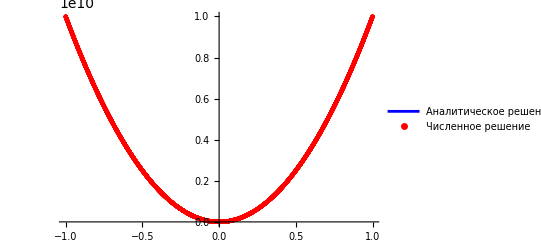

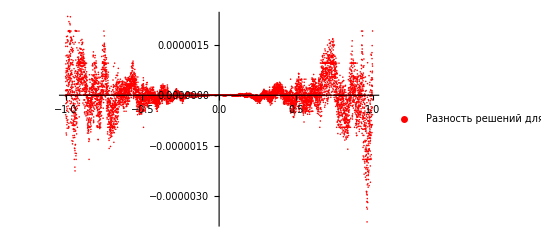

```mathematica
Show[Plot[f[x],{x,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Blue,PlotLegends->{"Аналитическое решение"}],ListPlot[data,PlotStyle->{Red,PointSize[Medium]},PlotLegends->{"Численное решение"}]]
ListPlot[differences,PlotStyle->Red,PlotRange->All,PlotLegends->{"Разность решений для"}]
```

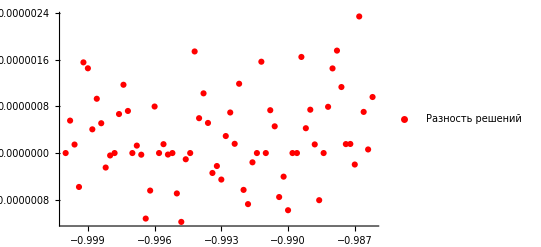

```mathematica
ListPlot[differences[[1;;70]],PlotStyle->Red,PlotRange->All,PlotLegends->{"Разность решений"}]
```

```mathematica
diffMoAFC=Total[(f[#]-#2)^2&@@@dataMoAFC]/Length[dataMoAFC]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
dataQ=Total[(f[#]-#2)^2&@@@dataQ]/Length[dataQ]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
differences
```

```mathematica
D[x^2+1/x,{x,2}]
```

2+2/x^3

```mathematica
Integrate[Sin[2x],x]
```

-1/2 Cos[2 x]

```mathematica
∑_(i=-l)^l 1
```

1+2 l

```mathematica
140*31*1.6*10^-13*31.536*10^6/140
```

0.000156419

```mathematica
31*140
```

4340